## This is a Tweak of LambertProjectionsNotebook.nb Focused on the Zodiac

Gall’s stereographic cylindrical projection results from projecting the earth’s surface from the equator onto a secant cylinder intersected by the globe at 45 degrees north and 45 degrees south. This projection moderately distorts distance, shape, direction, and area. Reference: The Geographer’s Craft

James Gall “USE OF CYLINDRICAL PROJECTIONS FOR GEOGRAPHICAL,
ASTRONOMICAL, AND SCIENTIFIC PURPOSES,” 1885 (reprinted from The Scottish Geographical Magazine).

Thorough, clear and mathematical Map Projections website by Carlos Furuti.

Image collage created using “Enhanced Geo Visualization” in accompanying PDF.

```mathematica
rightAscensionOffset = 90
```

90

```mathematica
styles[m_,n_]:=Table[{c,If[Mod[c,15]==0,Directive[Thick,Black],Directive[Thin, Black]]},{c,m,n,3}];
```

```mathematica
geoRange1={{-42.5,42.5},{0-rightAscensionOffset, 180 + rightAscensionOffset}}
```

{{-42.5,42.5},{-90,270}}

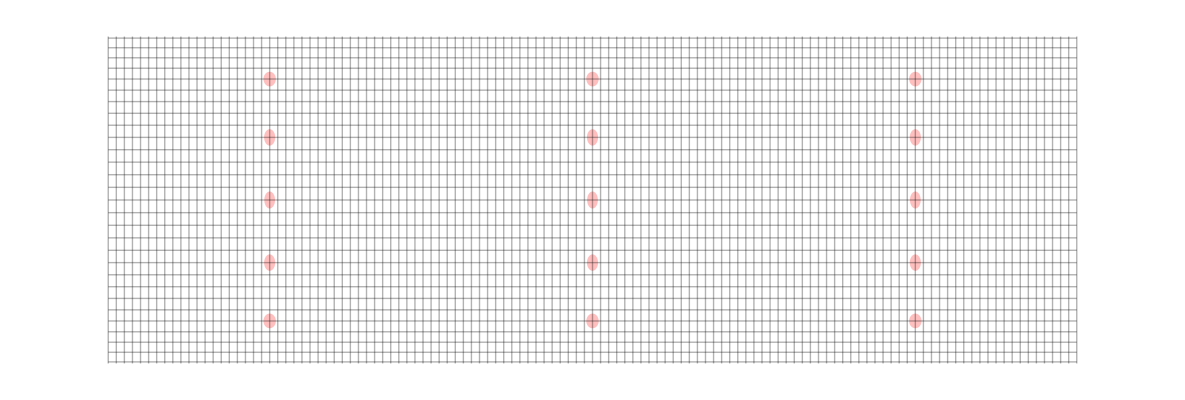

```mathematica
geoProjection1={"LambertCylindrical", "Centering"->GeoPosition[{0,90}]};GeoGraphics[{GeoStyling["OutlineMap",Directive[Pink,Opacity[0.5]]],GeoDisk[GeoPosition[#],Quantity[2,"AngularDegrees"]]&/@Flatten[Table[{90-15 * i,120*j -150},{i,1,12},{j,1,3}],1]},GeoProjection->geoProjection1, GeoRange->geoRange1, GeoGridLines->{styles[-42,42],styles[-57,300]}, GeoBackground->None]
```